# Regions 1

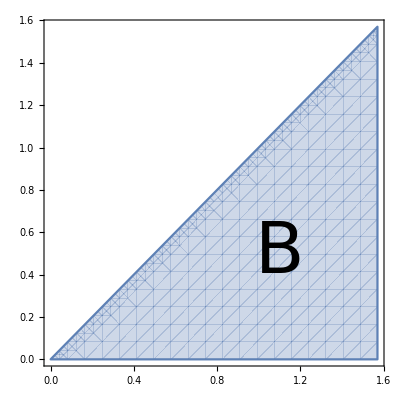

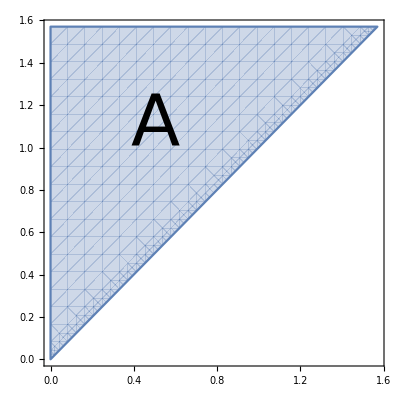

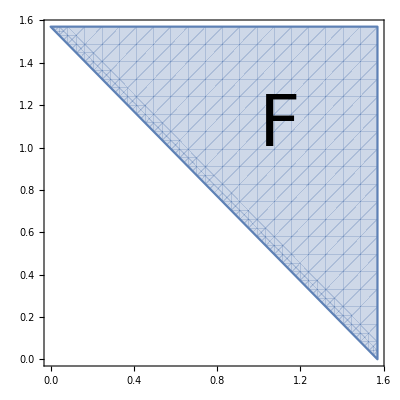

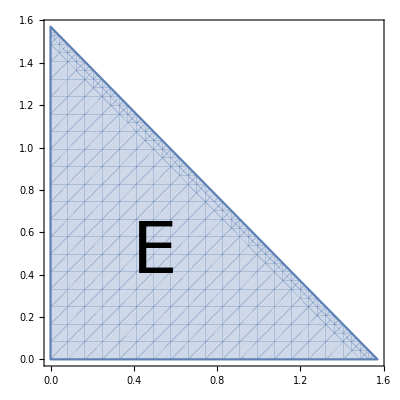

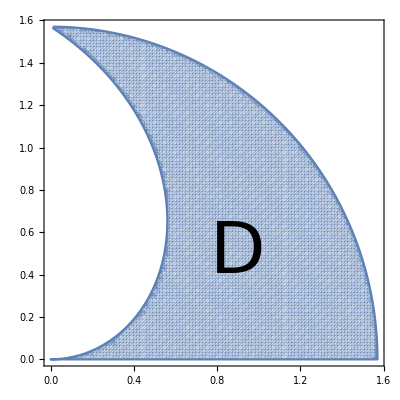

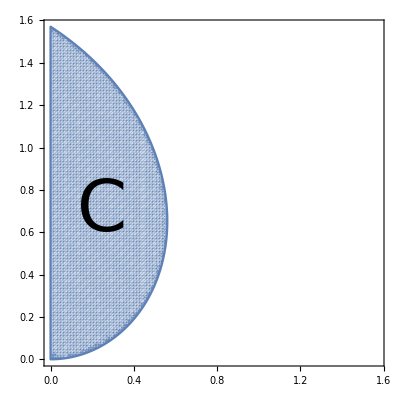

```mathematica
text=Graphics[
Text[Style["B",FontSize->100],{1.1,.5}],
FormatType->TraditionalForm];
region=RegionPlot[y<x<Pi/2&&0<y<Pi/2,{x,0,Pi/2},{y,0,Pi/2}];
region1=Show[region,text]


text=Graphics[
Text[Style["A",FontSize->100],{.5,1.1}],
FormatType->TraditionalForm];
region=RegionPlot[x<y<Pi/2&&0<x<Pi/2,{x,0,Pi/2},{y,0,Pi/2}];
region2=Show[region,text]


text=Graphics[
Text[Style["F",FontSize->100],{1.1,1.1}],
FormatType->TraditionalForm];
region=RegionPlot[0<y<Pi/2&&(Pi/2-y)<x<Pi/2,{x,0,Pi/2},{y,0,Pi/2}];
region3=Show[region,text]


text=Graphics[
Text[Style["E",FontSize->100],{.5,.5}],
FormatType->TraditionalForm];
region=RegionPlot[0<x<Pi/2&&0<y<Pi/2-x,{x,0,Pi/2},{y,0,Pi/2}];
region4=Show[region,text]


text=Graphics[
Text[Style["D",FontSize->100],{.9,.5}],
FormatType->TraditionalForm];
h[r_,t_]=t<r≤Pi/2&&0<t<Pi/2;
region=RegionPlot[h[Sqrt[x^2+y^2],ArcTan[x,y]],{x,0,Pi/2},{y,0,Pi/2},PlotPoints->100];
region5=Show[region,text]


text=Graphics[
Text[Style["C",FontSize->100],{.25,.7}],
FormatType->TraditionalForm];
h[r_,t_]=0<r≤Pi/2&&r<t<Pi/2;
region=RegionPlot[h[Sqrt[x^2+y^2],ArcTan[x,y]],{x,0,Pi/2},{y,0,Pi/2},PlotPoints->100];
region6=Show[region,text]
```

```mathematica
Export["~/teaching/2153/math2153/exams/exam2/sp17/region1.png",region1,ImageResolution->300]
Export["~/teaching/2153/math2153/exams/exam2/sp17/region2.png",region2,ImageResolution->300]
Export["~/teaching/2153/math2153/exams/exam2/sp17/region3.png",region3,ImageResolution->300]
Export["~/teaching/2153/math2153/exams/exam2/sp17/region4.png",region4,ImageResolution->300]
Export["~/teaching/2153/math2153/exams/exam2/sp17/region5.png",region5,ImageResolution->300]
Export["~/teaching/2153/math2153/exams/exam2/sp17/region6.png",region6,ImageResolution->300]
```

~/teaching/2153/math2153/exams/exam2/sp17/region1.png

~/teaching/2153/math2153/exams/exam2/sp17/region2.png

~/teaching/2153/math2153/exams/exam2/sp17/region3.png

~/teaching/2153/math2153/exams/exam2/sp17/region4.png

~/teaching/2153/math2153/exams/exam2/sp17/region5.png

~/teaching/2153/math2153/exams/exam2/sp17/region6.png

# Regions 2

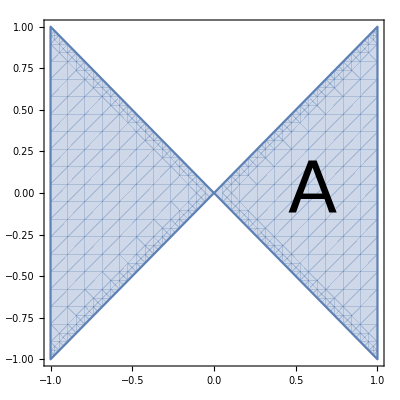

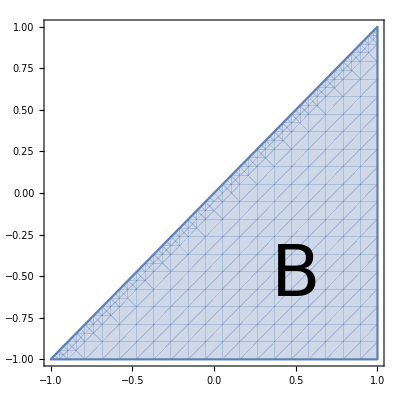

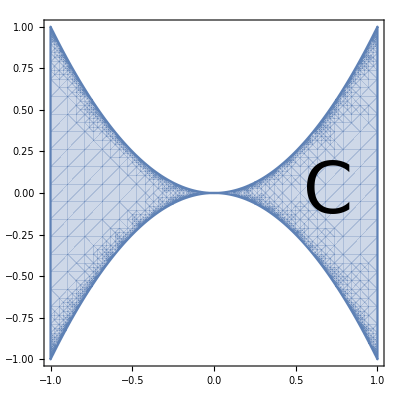

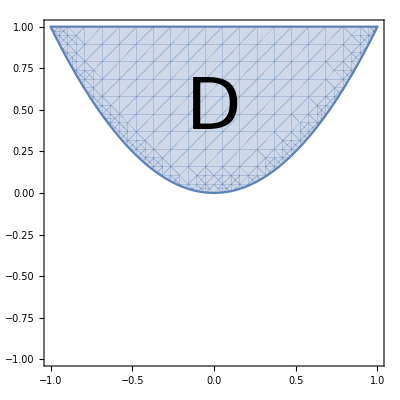

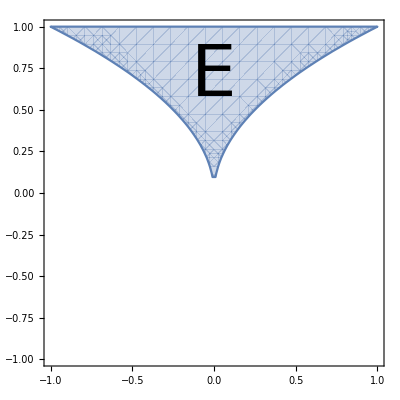

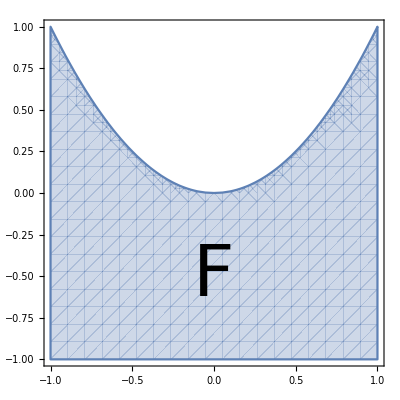

```mathematica
text=Graphics[
Text[Style["A",FontSize->100],{.6,0}],
FormatType->TraditionalForm];
region=RegionPlot[-1<x<1&&-Abs[x]<y<Abs[x],{x,-1,1},{y,-1,1}];
region1=Show[region,text]

text=Graphics[
Text[Style["B",FontSize->100],{.5,-.5}],
FormatType->TraditionalForm];
region=RegionPlot[-1<x<1&&-1<y<x,{x,-1,1},{y,-1,1}];
region2=Show[region,text]

text=Graphics[
Text[Style["C",FontSize->100],{.7,0}],
FormatType->TraditionalForm];
region=RegionPlot[-1<x<1&&-x^2<y<x^2,{x,-1,1},{y,-1,1},MaxRecursion->8];
region3=Show[region,text]


text=Graphics[
Text[Style["D",FontSize->100],{0,.5}],
FormatType->TraditionalForm];
region=RegionPlot[-1<x<1&&x^2<y<1,{x,-1,1},{y,-1,1}];
region4=Show[region,text]


text=Graphics[
Text[Style["E",FontSize->100],{0,.7}],
FormatType->TraditionalForm];
region=RegionPlot[-1<x<1&&Sqrt[Abs[x]]<y<1,{x,-1,1},{y,-1,1}];
region5=Show[region,text]

text=Graphics[
Text[Style["F",FontSize->100],{0,-.5}],
FormatType->TraditionalForm];
region=RegionPlot[-1<x<1&&-1<y<x^2,{x,-1,1},{y,-1,1}];
region6=Show[region,text]
```

```mathematica
Export["~/teaching/2153/math2153/exams/practice/exam2/region1a.png",region1,ImageResolution->300]
Export["~/teaching/2153/math2153/exams/practice/exam2/region2a.png",region2,ImageResolution->300]
Export["~/teaching/2153/math2153/exams/practice/exam2/region3a.png",region3,ImageResolution->300]
Export["~/teaching/2153/math2153/exams/practice/exam2/region4a.png",region4,ImageResolution->300]
Export["~/teaching/2153/math2153/exams/practice/exam2/region5a.png",region5,ImageResolution->300]
Export["~/teaching/2153/math2153/exams/practice/exam2/region6a.png",region6,ImageResolution->300]
```

~/teaching/2153/math2153/exams/practice/exam2/region1a.png

~/teaching/2153/math2153/exams/practice/exam2/region2a.png

~/teaching/2153/math2153/exams/practice/exam2/region3a.png

~/teaching/2153/math2153/exams/practice/exam2/region4a.png

~/teaching/2153/math2153/exams/practice/exam2/region5a.png

~/teaching/2153/math2153/exams/practice/exam2/region6a.png